```mathematica
FRS = StudentTDistribution[2,1,5];
FRF = NormalDistribution[2,1];
```

```mathematica
FRS = StudentTDistribution[0,0.01,5];
FRF = NormalDistribution[2,1];
```

```mathematica
c=CopulaDistribution[{"GumbelHougaard", 1}, {UniformDistribution[{0,1}], UniformDistribution[{0,1}]}];
```

```mathematica
(*FRS = NormalDistribution[0,1];
FRF = NormalDistribution[0,1];
c=CopulaDistribution[{"Binormal", 0.2}, {UniformDistribution[{0,1}], UniformDistribution[{0,1}]}];*)
```

```mathematica
(*FRS = NormalDistribution[2,1];
FRF = NormalDistribution[1,1];
c=CopulaDistribution[{"GumbelHougaard",1}, {UniformDistribution[{0,1}], UniformDistribution[{0,1}]}]; (* independence at theta=1 *)*)
```

```mathematica
h=1;
```

```mathematica
b0=0.0001; b1=0.5-b0; b2=0.5+b0; b3=1-b0;
```

```mathematica
CDF[FRF,l-InverseCDF[FRS,w2]]/.{w2->0.2, l->3}
```

0.84356

```mathematica
CDF[c, {0.2, 0.05}]
```

0.01

```mathematica
N[Simplify[CDF[c,{w,CDF[FRF,l-InverseCDF[FRS,w2]]}]/.{w2->0.2, w->0.2, l->2}]]
```

Greater::nord2: Comparison of erfc(0.0158114 √(-1+1/1.6)) and 2 is invalid.

0.100734

```mathematica
N[D[Simplify[CDF[c,{w,CDF[FRF,l-InverseCDF[FRS,w2]]}],Assumptions->{0<w<b1}], w]/.{w2->w,l->0}]/.w->0.3
```

0.0230539

```mathematica
NIntegrate[D[Simplify[CDF[c,{w,CDF[FRF,l-InverseCDF[FRS,w2]]}],Assumptions->{0<w<b1}], w]/.{w2->w,l->5},{w,b0,b1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.499523 and 0.000285314 for the integral and error estimates.

0.499523

F assumes that the difference bw r.v.’s is taken, whereas F1 and F2 assume that the sum of the  two  r.v.’s is taken

```mathematica
F[l_]:=1-(NIntegrate[D[Simplify[CDF[c,{w,CDF[FRF,(InverseCDF[FRS,w2]-l)/h]}],Assumptions->{0<w<b1}], w]/.w2->w,{w,b0,b1}]+NIntegrate[D[Simplify[CDF[c,{w,CDF[FRF,(InverseCDF[FRS,w2]-l)/h]}],Assumptions->{b2<w<1}], w]/.w2->w,{w,b2,b3}])
```

```mathematica
F1[l_]:=NIntegrate[D[Simplify[CDF[c,{w,CDF[FRF,l-InverseCDF[FRS,w2]]}],Assumptions->{0<w<b1}], w]/.w2->w,{w,b0,b1}]+NIntegrate[D[Simplify[CDF[c,{w,CDF[FRF,l-InverseCDF[FRS,w2]]}],Assumptions->{b2<w<1}], w]/.w2->w,{w,b2,b3}]
```

```mathematica
F2[l_]:=NIntegrate[CDF[FRF,l-x] PDF[FRS,x], {x,-20,20}]
```

The red curve matches the other ones only if the marginals are normally distributed and the independence copula (theta=1) is used.
Blue and red curves should match in case of difference. In case of sum of r.v.’s all curves should match.

```mathematica
ListPlot[Table[{l,F[l]}, {l,-8,8,.25}], Joined->True,PlotStyle->Darker[Blue]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.500178 and 0.000285501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.499822 and 0.000285501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.500178 and 0.000285501 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
Show[
ListPlot[Table[{l,F[l]}, {l,-8,8,.25}], Joined->True,PlotStyle->Darker[Blue]], 
ListPlot[Table[{l,F1[l]}, {l,-8,8,.25}], Joined->True,PlotStyle->Darker[Green]],
ListPlot[Table[{l,F2[l]}, {l,-8,8,.25}], Joined->True,PlotStyle->Darker[Orange]],
Plot[CDF[NormalDistribution[Mean[FRS]-h Mean[FRF],Sqrt[Variance[FRS]+h^2 Variance[FRF]]], l], {l,-8,8}, PlotStyle->Darker[Red]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.500178 and 0.000285501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.499822 and 0.000285501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.500178 and 0.000285501 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.499481 and 0.000285382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.499168 and 0.000285481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.497111}. NIntegrate obtained 0.496987 and 0.000284758 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

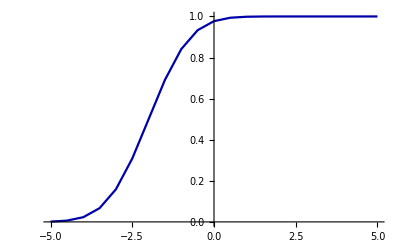

```mathematica
Show[
ListPlot[Table[{l,F[l]}, {l,-5,5,.5}], Joined->True,PlotStyle->Darker[Blue]]
]
```